```mathematica
sphereTangencyCondition[{x1_,y1_,z1_,r1_}]:= (x-x1)^2+(y-y1)^2+(z-z1)^2==(r1+r)^2;
pane1 =x == r;
pane2 =y  == r;
pane3 =z == r;
bigS = sphereTangencyCondition[{1,1,1,1}]
```

(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2

```mathematica
Table[slst =NSolve[{i[[1]],i[[2]],i[[3]],i[[4]]}];
slst = slst[[Position[r/.slst,Min[r/.slst]][[1]][[1]]]];{sphereTangencyCondition[{x,y,z,r}/.slst],i},{i,{{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,x==r,y==r,z==r},{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,2-x==r,y==r,z==r},{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,2-x==r,2-y==r,z==r},{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,x==r,y==r,2-z==r},{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,x==r,y==r,2-z==r},{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,2-x==r,y==r,2-z==r},{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,2-x==r,2-y==r,2-z==r},{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,x==r,2-y==r,2-z==r}}}]
```

{{(-0.267949+x)^2+(-0.267949+y)^2+(-0.267949+z)^2==(0.267949+r)^2,{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,x==r,y==r,z==r}},{(-1.73205+x)^2+(-0.267949+y)^2+(-0.267949+z)^2==(0.267949+r)^2,{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,2-x==r,y==r,z==r}},{(-1.73205+x)^2+(-1.73205+y)^2+(-0.267949+z)^2==(0.267949+r)^2,{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,2-x==r,2-y==r,z==r}},{(-0.267949+x)^2+(-0.267949+y)^2+(-1.73205+z)^2==(0.267949+r)^2,{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,x==r,y==r,2-z==r}},{(-0.267949+x)^2+(-0.267949+y)^2+(-1.73205+z)^2==(0.267949+r)^2,{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,x==r,y==r,2-z==r}},{(-1.73205+x)^2+(-0.267949+y)^2+(-1.73205+z)^2==(0.267949+r)^2,{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,2-x==r,y==r,2-z==r}},{(-1.73205+x)^2+(-1.73205+y)^2+(-1.73205+z)^2==(0.267949+r)^2,{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,2-x==r,2-y==r,2-z==r}},{(-0.267949+x)^2+(-1.73205+y)^2+(-1.73205+z)^2==(0.267949+r)^2,{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,x==r,2-y==r,2-z==r}}}

```mathematica
nextgen[lst_]:=Module[{slst,xx,yy,zz,rr,xxx,yyy,zzz,rrr,ieq, int,eq5,eq6,gg,ret,works,slst2,x2,y2,z2,r2,thesph},
Return[
Flatten[
Table[
Table[
ieq=sphereTangencyCondition[i[[1]]];
(*Print[j];*);
(*Print[ieq];*);
slst = NSolve[{j[[1]],j[[2]],j[[3]],ieq},{x,y,z,r}];
slst = slst[[Position[r/.slst,Min[Abs[r]/.slst]][[1]][[1]]]];
{xx,yy,zz,rr}={x,y,z,r}/.slst;
int=False;
If[xx-rr<0-10^-9,int=True;eq6=x==r,
If[xx+rr>2+10^-9,int=True;eq6=x==2-r,
If[yy-rr<0-10^-9,int=True;eq6=y==r,
If[yy+rr>2+10^-9,int=True;eq6=y==2-r,
If[zz-rr<0-10^-9,int=True;eq6=z==r,
If[zz+rr>2+10^-9,int=True;eq6=z==2-r,
];
];
];
];
];
];
If[!int,
Do[If[{xxx,yyy,zzz,rrr}=m[[1]];
(EuclideanDistance[{xxx,yyy,zzz},{xx,yy,zz}]<Abs[rrr]+Abs[rr]-1*10^-9),
int=True;
eq6=sphereTangencyCondition[m[[1]]];
Break[];],{m,gglist}];];

If[int,
eq5 = sphereTangencyCondition[{xx,yy,zz,rr}];
gg=False;
Do[
slst2 = NSolve[eeee,{x,y,z,r}];
(*Print[i];
Print["hi4"];*);
slst2 = slst2[[Position[r/.slst2,Min[Abs[r]/.slst2]][[1]][[1]]]];
(*Print["hi3"];*);
{x2,y2,z2,r2}={x,y,z,r}/.slst2;
works=True;
If[x2-r2<0-10^-9||x2+r2>2+10^-9||y2-r2<0-10^-9||y2+r2>2+10^-9||z2-r2<0-10^-9||z2+r2>2+10^-9,works=False];
If[works,
Do[
If[{xxx,yyy,zzz,rrr}=k[[1]];EuclideanDistance[{xxx,yyy,zzz},{x2,y2,z2}]<Abs[rrr]+Abs[r2]-1*10^-6,works=False;Break[];],{k,gglist}];];
If[works,thesph={{x2,y2,z2,r2},eeee};gg=True;Break[];],{eeee,{{j[[1]],j[[2]],j[[3]],eq6},{j[[1]],j[[2]],ieq,eq6},{j[[1]],j[[3]],ieq,eq6},{j[[2]],j[[3]],ieq,eq6}}}];
If[gg,ret=thesph;
,ret=Nothing]
,
(*else:*)
ret={{xx,yy,zz,rr},{j[[1]],j[[2]],j[[3]],ieq}};
];
AppendTo[gglist,ret];
ret
,
{j,Subsets[i[[2]],{3}]}
],
{i,lst}
],1
]
]
]
```

```mathematica
cg[gen_]:=Module[{lst},
glist={{{{1,1,1,1}}}};
lst=Table[slst =NSolve[{i[[1]],i[[2]],i[[3]],i[[4]]}];
slst = slst[[Position[r/.slst,Min[Abs[r]/.slst]][[1]][[1]]]];{{x,y,z,r}/.slst,i},{i,{{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,x==r,y==r,z==r},{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,2-x==r,y==r,z==r},{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,2-x==r,2-y==r,z==r},{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,x==r,y==r,2-z==r},{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,x==r,2-y==r,z==r},{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,2-x==r,y==r,2-z==r},{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,2-x==r,2-y==r,2-z==r},{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,x==r,2-y==r,2-z==r}}}];
gglist=Join[gglist,lst];
glist = Join[glist,{lst}];
For[i=0,i<gen,i++,
lst=nextgen[lst];
glist = Join[glist,{lst}];
AppendTo[sumlist,Total[Table[4/3*Pi*(i[[1]][[4]])^3,{i,lst}]]];
];
]
```

```mathematica
gglist={};
glist={};
sumlist={};
cg[4];
```

```mathematica
sumlist
```

{0.66666,0.454272,0.468104,0.30286}

```mathematica
8*{4/3*Pi*(2-√3)^3,0.0833325,0.10810320139515608,0.06268294331557804,0.05353659659345511,0.03349610553883636}
```

{32/3 (2-√3)^3 π,0.66666,0.864826,0.501464,0.428293,0.267969}

```mathematica
Accumulate[{4/3*Pi,32/3 (2-√3)^3 π,0.66666,0.8648256111612487,0.5014635465246243,0.4282927727476409,0.2679688443106909}]
```

{(4 π)/3,(4 π)/3+32/3 (2-√3)^3 π,5.50012,6.36494,6.86641,7.2947,7.56267}

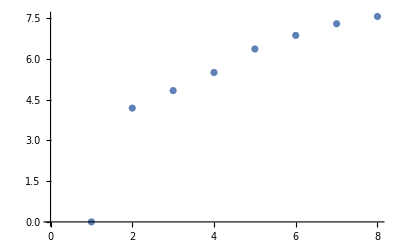

```mathematica
ListPlot[{0,(4 π)/3,(4 π)/3+32/3 (2-√3)^3 π,5.500117967931148,6.3649435790923965,6.8664071256170205,7.294699898364661,7.562668742675353}]
```

```mathematica
Total[Table[i[[1]][[3]],{i,lst}]]
```

Table::iterb: Iterator {i,lst} does not have appropriate bounds.

Total[Table[i⟦1⟧⟦3⟧,{i,lst}]]

```mathematica
glist
```

```mathematica
ColorData[97,"ColorList"][[1]]
```

RGBColor[0.368417, 0.506779, 0.709798]

```mathematica
Reverse[DataPaclets`ColorData`GetBlendArgument["Rainbow"][[1;;;;3]]]
```

{RGBColor[0.878107, 0.293208, 0.160481],RGBColor[0.863512, 0.670771, 0.236564],RGBColor[0.607651, 0.743718, 0.358588],RGBColor[0.36048, 0.655759, 0.645692],RGBColor[0.24408, 0.361242, 0.816084],RGBColor[0.471412, 0.108766, 0.527016]}

```mathematica
colours={Red,Orange,Yellow,Green,Blue,Purple};
n=0;
llll=Table[++n;Table[{colours[[n]],Sphere[{i[[1]][[1]],i[[1]][[2]],i[[1]][[3]]},i[[1]][[4]]]},{i,j}],{j,glist}];
manip=Manipulate[Show[Graphics3D[llll[[1;;f]]]],{{f,Length[llll]},Range[Length[llll]]}]
```

```mathematica
(*Export["cganim.mp4",manip]*)
```